# Lista 3

## Exercise 1

## Exercise 2

## Exercise 3

We want to compute rankt of the matrices and find their biggest minor:

```mathematica
M1={{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}
MatrixRank[M1]
Minors[M1,MatrixRank[M1]]
```

{{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

```mathematica
M2={{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}
MatrixRank[M2]
Minors[M1,MatrixRank[M2]]
```

{{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

## Exercise 4

## Exercise 5

We want to compute rankt of the matrix:

```mathematica
la={{7-λ,-12,6},{10,-λ-19,10},{12,-24,13-λ}}
MatrixRank[la]
```

{{7-λ,-12,6},{10,-19-λ,10},{12,-24,13-λ}}

3

## Exercise 6

{Tirana,Andorra la Vella,Vienna,Minsk,Brussels,Sarajevo,Sofia,Zagreb,Nicosia,Prague,Copenhagen,Tallinn,Torshavn,Helsinki,Paris,Berlin,Gibraltar,Athens,Saint Peter Port,Budapest,Reykjavik,Dublin,Douglas,Rome,Saint Helier,Pristina,Riga,Vaduz,Vilnius,Luxemburg,Skopje,Valletta,Chisinau,Monaco-Ville,Podgorica,Amsterdam,Oslo,Warsaw,Lisbon,Bucharest,San Marino,Belgrade,Bratislava,Ljubljana,Madrid,Longyearbyen,Stockholm,Bern,Kyiv,London,Vatican City}

{Tirana,AndorraLaVella,Vienna,Minsk,Brussels,Sarajevo,Sofia,Zagreb,Nicosia,Prague,Copenhagen,Tallinn,Torshavn,Helsinki,Paris,Berlin,Gibraltar,Athens,SaintPeterPort,Budapest,Reykjavik,Dublin,Douglas,Rome,SaintHelier,Pristina,Riga,Vaduz,Vilnius,Luxemburg,Skopje,Valletta,Chisinau,MonacoVille,Podgorica,Amsterdam,Oslo,Warsaw,Lisbon,Bucharest,SanMarino,Belgrade,Bratislava,Ljubljana,Madrid,Longyearbyen,Stockholm,Bern,Kiev,London,VaticanCity}

{18.,13.9,3.6,5.,14.6,7.,11.,11.,23.4,1.,6.,9.,5.6,9.,13.,4.4,18.5,19.6,14.,6.4,3.,10.,11.,17.,14.,8.7,8.,7.6,3.,9.,9.,22.,11.,18.,14.3,12.,4.3,8.,16.6,15.,11.7,7.6,7.7,8.3,12.,-5.9,9.,9.,10.,13.,17.}

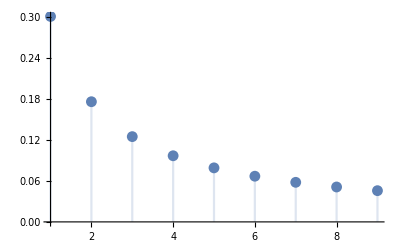

```mathematica
TmpCapt=CountryData["Europe","CapitalCity"]
TC=Table[TmpCapt[[i]][[2]][[1]],{i,1,Length[TmpCapt]}]
tc[u_]:=WeatherData[u,"Temperature"]
FinalCT=Map[tc,TC]
```

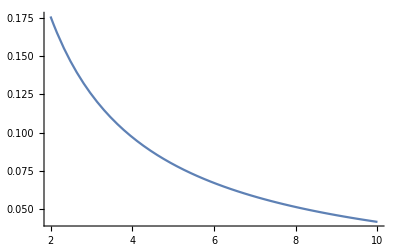

-Graphics-

```mathematica
Plot[Log10[1+1/x],{x,2,10}]
DiscretePlot[Log10[1+1/i],{i,1,9}]
```

```mathematica
Pop=CountryData[,"Population"]
```

## Exercise 7

## Exercise 8

## Exercise 9